```mathematica
v1[x1_]=A1 Cos[Sqrt[P/EI] x1]+A2 Sin[Sqrt[P/EI] x1]+A3+A4 x1
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

A3+A4 x1+A1 Cos[√(P/EI) x1]+A2 Sin[√(P/EI) x1]

```mathematica
v2[x2_]=B1 x2^3+B2 x2^2+B3 x2+B4
```

B4+B3 x2+B2 x2^2+B1 x2^3

```mathematica
system={v1[0]==0,v1'[0]==0,v1[H]==0,v1'[H]==v2'[0],v1''[H]==v2''[0],v2[0]==0,v2[B]==0,v2'[B]==0}//FullSimplify
```

{A1+A3==0,A4+A2 √(P/EI)==0,A3+A4 H+A1 Cos[H √(P/EI)]+A2 Sin[H √(P/EI)]==0,A4+√(P/EI) (A2 Cos[H √(P/EI)]-A1 Sin[H √(P/EI)])==B3,-(P (A1 Cos[H √(P/EI)]+A2 Sin[H √(P/EI)]))/EI==2 B2,B4==0,B (B (B B1+B2)+B3)+B4==0,3 B^2 B1+2 B B2+B3==0}

```mathematica
dd=Det[Normal[CoefficientArrays[system,{A1,A2,A3,A4,B1,B2,B3,B4}]][[2]]]//FullSimplify
```

(B^3 (-8 EI √(P/EI)+√(P/EI) (8 EI+B H P) Cos[H √(P/EI)]-(B-4 H) P Sin[H √(P/EI)]))/EI

```mathematica
dd/.P->α^2/H^2*EI//FullSimplify
```

(B^3 √(α^2/H^2) (-8 H+(8 H+B α^2) Cos[α]-(B-4 H) α Sin[α]))/H

```mathematica
(-8 H+(8 H+B α^2) Cos[α]-(B-4 H) α Sin[α])/H
```

-8+8 Cos[α]+(B α^2 Cos[α])/H+4 α Sin[α]-(B α Sin[α])/H

```mathematica
Solve[x Cos[x]==Sin[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x Cos[x]==Sin[x],x]

```mathematica
Solve[x*Cos[x]==Sin[x],x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x Cos[x]==Sin[x],x]

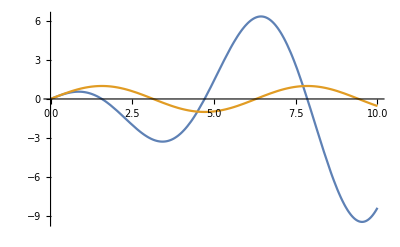

```mathematica
Plot[{x*Cos[x],Sin[x]},{x,0,10}]
```

```mathematica
1/N[25/Pi^2]
```

0.394784